```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\work\critical_region\LPA\runningpoint\nu\phase\LPA_Tscaling_mub716p662_fpi\buffer

```mathematica
fpi=Flatten[Import["./fpi.dat"]];
ms=Flatten[Import["./mSigma.dat"]];
mp=Flatten[Import["./mPion.dat"]];
cl=Flatten[Import["./TMeV.dat"]];
t=-((cl-cl[[1]])/cl[[1]]);
csdata=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
a1=Table[FindFit[csdata[[i-1;;i+1]],a+b x,{a,b},x][[1]][[2]],{i,2,Length[cl]-2}];
b1600=Table[FindFit[csdata[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[cl]-2}];
Show[ListPlot[Transpose[{cl,fpi}],PlotRange->All]]
```

Import::nffil: 在 Import 期间没有找到文件 ./fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./mSigma.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./mPion.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 3.

-Graphics-

```mathematica
Show[ListPlot[{Transpose[{cl,ms}],Transpose[{cl,mp}]},PlotRange->All]]
```

-Graphics-

```mathematica
k=Flatten[Import["k1.dat"]];
kappa=Flatten[Import["y13.dat"]];
```

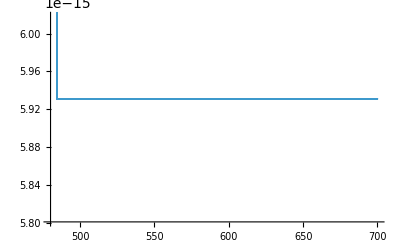

```mathematica
ListPlot[Transpose[{k,kappa}]]
```